### Two-mode Squeezed state as input 2019/08/30 2019/06/04

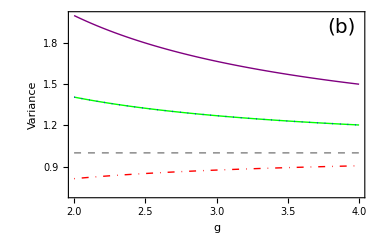

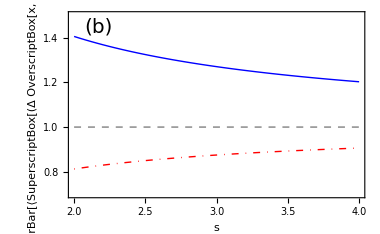

```mathematica
n=50;(* number od modes *)
T=1/(n s);
fX2=1+2 n T(Sinh[r]^2);(* Without wavefront shaping*)
fP2=1+2 n T(Sinh[r]^2);(* Without wavefront shaping*)
flucX2=1+2 n T Sinh[r](Sinh[r]-π/4 Cosh[r]);(* With wavefront shaping*)
flucP2=1+2 n T Sinh[r](Sinh[r]+π/4 Cosh[r]);(* With wavefront shaping*)
fig4=Plot[{flucX2/.r->0.6,flucP2/.r->0.6,fX2/.r->0.6,fP2/.r->0.6,s-s+1},{s,2,4},PlotStyle->{{DotDashed,Red,Thick},{Purple,Thick},{Green,Thick},{Dotted,Blue,Thick},{Gray,Dashed,Thick}},(*PlotLegends->Placed[{Style["(p̂)_b",FontSize->14],Style["(x̂)_b",FontSize->14],Style["(p̂)_b^w",FontSize->14],Style["(x̂)_b^w",FontSize->14],Style["SNL",FontSize->12.5]},{{0.89,0.58}}],*)Frame->True, FrameLabel->{Style["g",FontSize->20],Text[Style["Variance",FontSize->20]]},FrameTicksStyle->Directive[14.5],PlotRange->{{0.7,2}},Epilog->{Text[Style["(b)",FontSize->20],Scaled[{.92,.92}]]},ImageSize->{380,280}]
(*fig4=Plot[{fX2/.r->0.6,flucX2/.r->0.6,1+r-r},{s,2,4},PlotStyle->{{Blue,Thick},{DotDashed,Red,Thick},{Gray,Dashed,Thick}},(*PlotLegends->Placed[{Style["Without WS",FontSize->14],Style["With WS",FontSize->14],Style["SNL",FontSize->14]},{{0.75,0.75}}],*)Frame->True, FrameLabel->{Style["s",FontSize->20],Text[Style["OverBar[⟨SuperscriptBox[(ΔOverscriptBox[x, ^]), 2]⟩]",FontSize->20]]},FrameTicksStyle->Directive[14.5],PlotRange->{{0.7,1.5}},Epilog->{Text[Style["(b)",FontSize->20],Scaled[{.1,.92}]]},ImageSize->{380,280}]*)
```

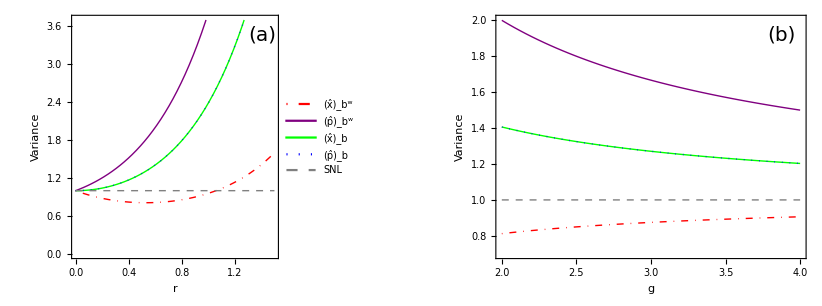

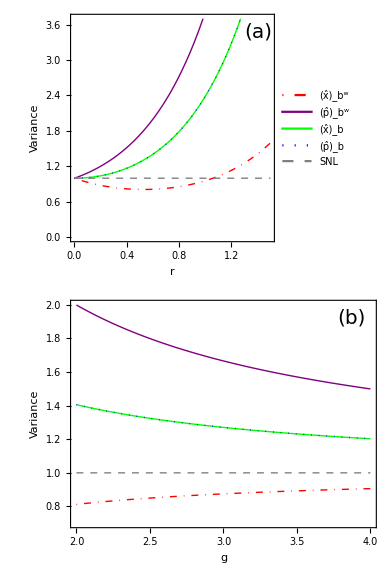

```mathematica
f24a=GraphicsGrid[{{fig2,fig4}}]
f24b=GraphicsGrid[{{fig2},{fig4}},Spacings->Scaled[.00]]
```

E:\MT\00_Researching\03_PUF\03_Security_PUF\05_New_scheme\09_Squeezing_focused_light\03_Code\00_Figures\sqz2a20190830.eps

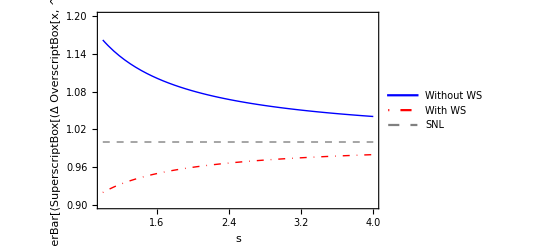

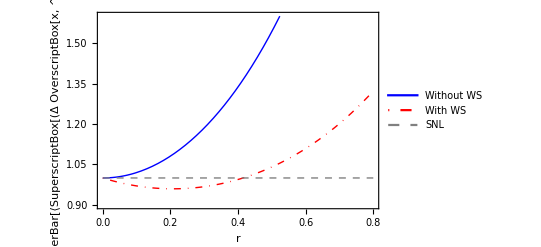

```mathematica
Export["E:\\MT\\00_Researching\\03_PUF\\03_Security_PUF\\05_New_scheme\\09_Squeezing_focused_light\\03_Code\\00_Figures\\sqz2a20190830.eps",f24b]
```

```mathematica
Export["E:\\MT\\00_Researching\\03_PUF\\03_Security_PUF\\05_New_scheme\\09_Squeezing_focused_light\\03_Code\\00_Figures\\dx2s_2modes20190604.eps",fig4](*ImageResolution->300,ImageSize->{480,480}];*)
```

E:\MT\00_Researching\03_PUF\03_Security_PUF\05_New_scheme\09_Squeezing_focused_light\03_Code\00_Figures\dx2s_2modes20190604.eps

```mathematica
GraphicsGrid[{{fig3},{fig4}}]
```

```mathematica
∫_0^∞ x/a^2 ⅇ^(-x^2/(2 a^2))ⅆx
```

ConditionalExpression[1,Re[a^2]>0]

```mathematica
f1=Simplify[∫_0^∞ x^(3/2)/a^2 ⅇ^(-x^2/(2 a^2))ⅆx,Assumptions->{a>0}]
```

2^(1/4) √a Gamma[5/4]

a √(π/2)

2 a^2

π/4

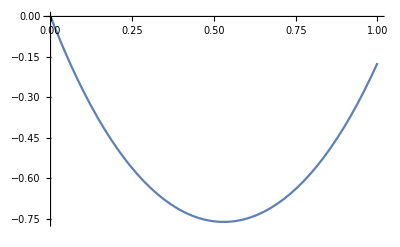

```mathematica
f2=Simplify[∫_0^∞ x^2/a^2 ⅇ^(-x^2/(2 a^2))ⅆx,Assumptions->{a>0}]
f4=Simplify[∫_0^∞ x^3/a^2 ⅇ^(-x^2/(2 a^2))ⅆx,Assumptions->{a>0}]
ratio=f2^2/f4  
diff=4Sinh[r](Sinh[r]-ratio Cosh[r]);
Plot[diff,{r,0,1}]
```

```mathematica
f4=Simplify[∫_0^∞ x^3/a^2 ⅇ^(-x^2/(2 a^2))ⅆx,Assumptions->{a>0}]
```

2 a^2

```mathematica
f6=Simplify[∫_0^∞ x^5/a^2 ⅇ^(-x^2/(2 a^2))ⅆx,Assumptions->{a>0}]
```

8 a^4

```mathematica
f6/f4^2
```

2

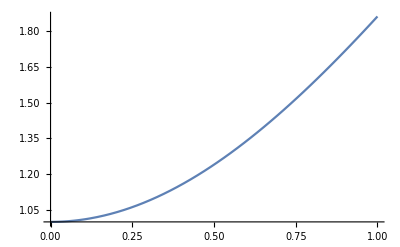

```mathematica
g=1/2 ⅇ^(-a^2) (2+a ⅇ^(a^2) √π+a ⅇ^(a^2) √π Erf[a]-a ⅇ^(a^2) √π Erfc[a]);
Plot[g,{a,0,1}]
```

1/2 (1+2 a^2) √π

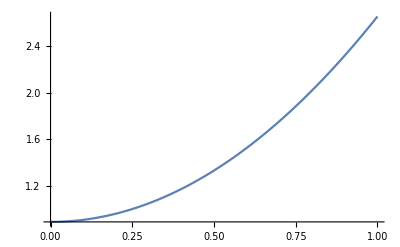

```mathematica
f1=1/(√π)∫_(-∞)^∞ x^2 ⅇ^(-(x-a)^2)ⅆx
Plot[f1,{a,0,1}]
```

```mathematica
norm=1/(√π)∫_(-∞)^∞ ⅇ^(-(x-a)^2)ⅆx
```

√π

1/4 (3+4 a^2 (3+a^2)) √π

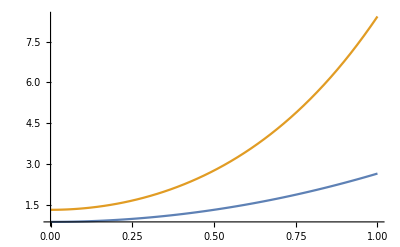

```mathematica
f2=∫_(-∞)^∞ x^4 ⅇ^(-(x-a)^2)ⅆx
Plot[{f1,f2},{a,0,1}]
```

```mathematica
√π f2/f1^2//Expand
```

3/((1+2 a^2)^2)+(12 a^2)/((1+2 a^2)^2)+(4 a^4)/((1+2 a^2)^2)

```mathematica
Sinh[x]/Cosh[x]
```

```mathematica
Tanh[x]
```

```mathematica
ArcTanh[Pi/8]//N
```

0.414987